```mathematica
FullSimplify[Solve[1-(d^2 √(1+d^2))/((d^2+(u-1)^2)^(3/2))==0,u],Assumptions->d>0]
```

{{u→1-√(-1+(1+1/d^2)^(1/3)) d},{u→1+√(-1+(1+1/d^2)^(1/3)) d}}

```mathematica
%/.d->1.
```

{{u→0.490175},{u→1.50982}}

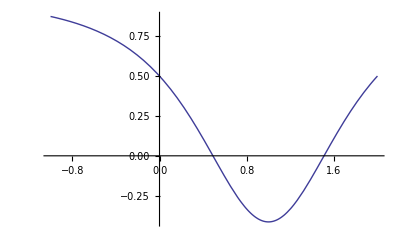

```mathematica
Plot[1-(d^2 √(1+d^2))/((d^2+(u-1)^2)^(3/2))/.d->1,{u,-1,2}]
```